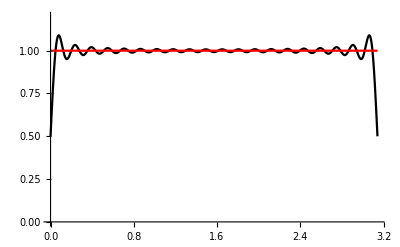

```mathematica
(*Problem #7 part a*)
(*Plot the Fourier Series f[x] = 1 on the interval [-L,L]*)
Clear[a,b,M,x,n,L,f, myFCos,myFSin,myFourier]
a[n_]:=Integrate[f[x]*Cos[(n*Pi/L)*x],{x,0,L}]*(1/L)
b[n_]:=Integrate[f[x]*Sin[(n*Pi/L)*x],{x,0,L}]*(1/L)
f[x_]=1;
L=Pi;

a[n];
b[n];

Table[a[n],{n,0,10}];
Table[b[n],{n,0,10}];

(*Below are the fourier cosine & sine series definitions*)
myFCos[x_,M_]:=Sum[a[n]*Cos[(n*Pi/L)*x],{n,1,M}]+a[0]/2
myFSin[x_,M_]:=Sum[b[n]*Sin[(n*Pi/L)*x],{n,1,M}]

(*Here is the fourier series definition*)
myFourier[x_,M_]:=Sum[a[n]*Cos[(n*Pi/L)*x]+b[n]*Sin[(n*Pi/L)*x],{n,1,M}]+a[0]/2

Plot[{Evaluate[myFourier[x,40]],f[x]},{x,0,L},PlotStyle->{Black,Red},PlotRange->{0,1.2}]
(*Graph of part a f(x) = 1*)
```

(4 n π Cos[n π]+2 (-2+n^2 π^2) Sin[n π])/(n^3 π)

0

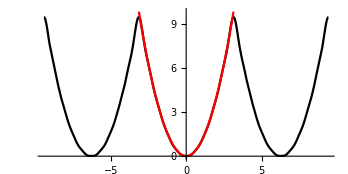

```mathematica
(*Problem #7 part b f(x) = x^2*)
Clear[a,b,M,x,n,L,f, myFCos,myFSin,myFourier]
a[n_]:=Integrate[f[x]*Cos[(n*Pi/L)*x],{x,-L,L}]*(1/L)
b[n_]:=Integrate[f[x]*Sin[(n*Pi/L)*x],{x,-L,L}]*(1/L)
f[x_]=x^2;
L=Pi;
a[n]
b[n]

(*Below are the fourier cosine & sine series definitions*)
myFCos[x_,M_]:=Sum[a[n]*Cos[(n*Pi/L)*x],{n,1,M}]+a[0]/2
myFSin[x_,M_]:=Sum[b[n]*Sin[(n*Pi/L)*x],{n,1,M}]

(*Here is the fourier series definition*)
myFourier[x_,M_]:=Sum[a[n]*Cos[(n*Pi/L)*x]+b[n]*Sin[(n*Pi/L)*x],{n,1,M}]+a[0]/2


Plot[{Evaluate[myFourier[x,10]],f[x]},{x,-3L,3L},PlotStyle->{Black,Red},PlotRange->{-0.01,f[L]},AspectRatio->1/2]
```

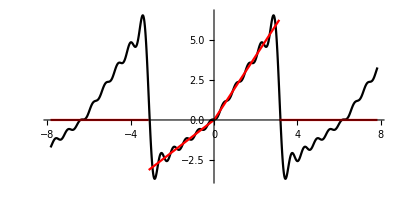

```mathematica
(*Problem #7 part c f(x) is a piecewise defined function*)
Clear[a,b,M,x,n,L,f, myFCos,myFSin,myFourier]
a[n_]:=Integrate[f[x]*Cos[(n*Pi/L)*x],{x,-L,L}]*(1/L)
b[n_]:=Integrate[f[x]*Sin[(n*Pi/L)*x],{x,-L,L}]*(1/L)
f[x_]:=Piecewise[{{x,x>=-L&&x<0},{2x,x>0&&x<=L}}]
L=Pi;

a[n];
b[n];

(*Below are the fourier cosine & sine series definitions*)
myFCos[x_,M_]:=Sum[a[n]*Cos[(n*Pi/L)*x],{n,1,M}]+a[0]/2
myFSin[x_,M_]:=Sum[b[n]*Sin[(n*Pi/L)*x],{n,1,M}]

(*Here is the fourier series definition*)
myFourier[x_,M_]:=Sum[a[n]*Cos[(n*Pi/L)*x]+b[n]*Sin[(n*Pi/L)*x],{n,1,M}]+a[0]/2


Plot[{Evaluate[myFourier[x,10]],f[x]},{x,-2.5L,2.5L},PlotStyle->{Black,Red},PlotRange->{f[-L]-.6,f[L]+.4},AspectRatio->1/2]
(*Graph of part c f(x) = piecewise*)
(*Notice that the periodicity of the 'x' part and '2x' are 
not the same*)
```

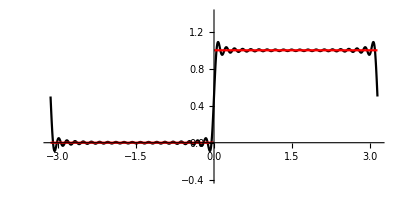

```mathematica
(*Problem #7 part d f(x) is a piecewise defined function*)
Clear[a,b,M,x,n,L,f, myFCos,myFSin,myFourier]
a[n_]:=Integrate[f[x]*Cos[(n*Pi/L)*x],{x,-L,L}]*(1/L)
b[n_]:=Integrate[f[x]*Sin[(n*Pi/L)*x],{x,-L,L}]*(1/L)
f[x_]:=Piecewise[{{0,x>=-L&&x<0},{1,x>0&&x<=L}}]
L=Pi;

a[n];
b[n];

(*Below are the fourier cosine & sine series definitions*)
myFCos[x_,M_]:=Sum[a[n]*Cos[(n*Pi/L)*x],{n,1,M}]+a[0]/2
myFSin[x_,M_]:=Sum[b[n]*Sin[(n*Pi/L)*x],{n,1,M}]

(*Here is the fourier series definition*)
myFourier[x_,M_]:=Sum[a[n]*Cos[(n*Pi/L)*x]+b[n]*Sin[(n*Pi/L)*x],{n,1,M}]+a[0]/2


Plot[{Evaluate[myFourier[x,40]],f[x]},{x,-L,L},PlotStyle->{Black,Red},PlotRange->{f[-L]-.4,f[L]+.4},AspectRatio->1/2]
(*Graph of part d piecewise*)
(*Notice that the graph switches form 0 and 1 at the origin*)
```